```mathematica
xcl[NN_,x0_,dotx0_]=x0+dotx0/(3H)(1-E^(-3NN));
Px[x_,NN_,x0_,dotx0_]=1/Sqrt[2π(H/(2π))^2 NN](Exp[(-(x-xcl[NN,x0,dotx0])^2)/(2(H/(2π))^2 NN)]-Exp[(-(x+xcl[NN,x0,dotx0])^2)/(2(H/(2π))^2 NN)])//Simplify
```

((ⅇ^(-(2 π^2 ((dotx0-dotx0 ⅇ^(-3 NN))/(3 H)-x+x0)^2)/(H^2 NN))-ⅇ^(-(2 π^2 ((dotx0-dotx0 ⅇ^(-3 NN))/(3 H)+x+x0)^2)/(H^2 NN))) √(2 π))/(√(H^2 NN))

```mathematica
Simplify[D[D[(1/Sqrt[2π s^2](Exp[(-(x-xc)^2)/(2 s^2)]-Exp[(-(x+xc)^2)/(2 s^2)])), x], x],{s>0}]
```

(ⅇ^(-(x+xc)^2/(2 s^2)) (-((-1+ⅇ^((2 x xc)/s^2)) s^2)+(-1+ⅇ^((2 x xc)/s^2)) x^2-2 (1+ⅇ^((2 x xc)/s^2)) x xc+(-1+ⅇ^((2 x xc)/s^2)) xc^2))/(√(2 π) s^5)

```mathematica
Px[0,NN,x0,dotx0]
```

0

```mathematica
S[NN_,x0_,dotx0_]=Integrate[1/Sqrt[2π s^2](Exp[(-(x-xc)^2)/(2 s^2)]-Exp[(-(x+xc)^2)/(2 s^2)]),{x,-∞,0},Assumptions->{s>0,xc<0}]/.{s->H/(2π)Sqrt[NN],xc->xcl[NN,x0,dotx0]}//Simplify
```

-Erf[(√2 π (dotx0-dotx0 ⅇ^(-3 NN)+3 H x0))/(3 H^2 √NN)]

```mathematica
PFPTwoNorm[NN_,x0_,dotx0_]=-D[S[NN,x0,dotx0], NN]//Simplify
```

-(ⅇ^(-3 NN-(2 π^2 (dotx0-dotx0 ⅇ^(-3 NN)+3 H x0)^2)/(9 H^4 NN)) √(2 π) (dotx0 (-1+ⅇ^(3 NN)-6 NN)+3 ⅇ^(3 NN) H x0))/(3 H^2 NN^(3/2))

```mathematica
Hs=10^-8;
calPf=1/(2ϵfss)(Hs/(2π))^2
```

1/(80000000000000000 π^2 ϵfss)

```mathematica
ϵfs=ϵfss/.Solve[calPf==10^-2,ϵfss][[1]]
```

1/(800000000000000 π^2)

```mathematica
ϵis=10^-2;
```

```mathematica
Nfs=Log[ϵis/ϵfs]/6;Nfs//N
```

5.33332

```mathematica
dotx0s=dotx0ss/.Solve[ϵis==dotx0ss^2/(2 Hs^2),dotx0ss][[2]]
dotxfs=dotxfss/.Solve[ϵfs==dotxfss^2/(2 Hs^2),dotxfss][[2]]
```

1/(500000000 √2)

1/(2000000000000000 π)

```mathematica
x0s=-(dotx0s-dotxfs)/(3Hs)
```

-100000000/3 (1/(500000000 √2)-1/(2000000000000000 π))

```mathematica
params={H->Hs,dotx0->dotx0s,x0->x0s,Nf->Nfs}
```

{H→1/100000000,dotx0→1/(500000000 √2),x0→-100000000/3 (1/(500000000 √2)-1/(2000000000000000 π)),Nf→1/6 Log[8000000000000 π^2]}

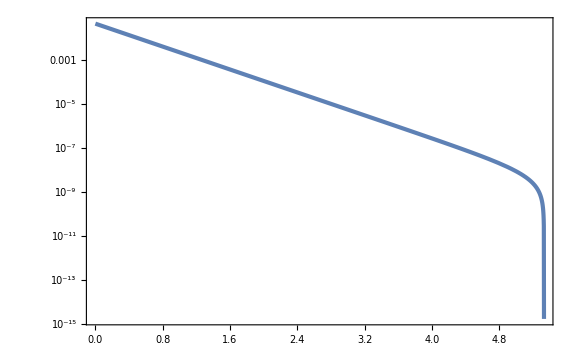

```mathematica
LogPlot[Abs[xcl[NN,x0s,dotx0s]]/.params,{NN,0,Nf/.params}]
```

General::munfl: Exp[-5.39018×10^9] is too small to represent as a normalized machine number; precision may be lost.

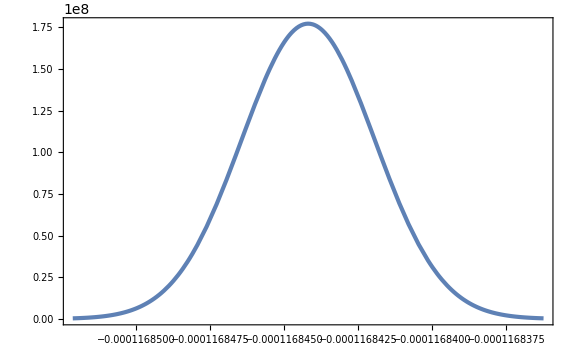

```mathematica
Plot[Px[x,2,x0s,dotx0s]/.params,{x,xcl[2,x0s,dotx0s]-5 H/(2π)/.params,xcl[2,x0s,dotx0s]+5 H/(2π)/.params}]
```

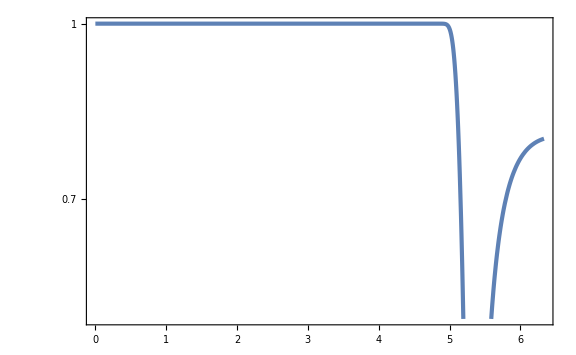

```mathematica
LogPlot[Abs[S[NN,x0s,dotx0s]]/.params,{NN,0,Nf+1/.params}]
```

```mathematica
NormS=NIntegrate[S[NN,x0s,dotx0s]/.params,{NN,0,20}]
```

-4.35459

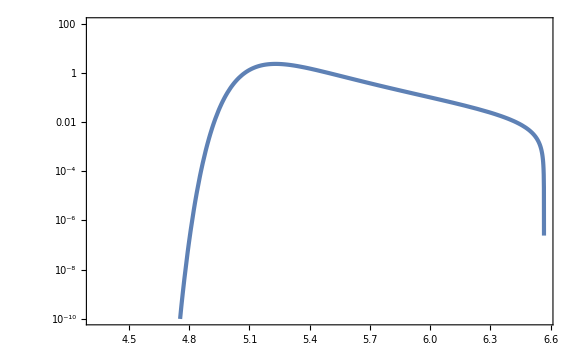

```mathematica
LogPlot[PFPTwoNorm[NN,x0s,dotx0s]/NormS/.params,{NN,Nf-1/.params,Nf+2/.params},PlotRange->{10^-10,10^2},GridLines->{{Nf/.params},None}]
```

```mathematica
NIntegrate[PFPTwoNorm[NN,x0s,dotx0s]/NormS/.params,{NN,0,10}]
```

0.947948